```mathematica
(* 未经作者同意请不要复制或转载本文任何内容 *)
(* @By wuwc *)
(* @EMail: brucecen2@gmail.com *)
```

```mathematica
(*
F(r)=dU/dr;
Lennard Jonus potential
U(r) = 4ϵ((σ/r)^12-(σ/r)^6);
σ is size of atom;
*)
```

General::ivar: 0.0362214 is not a valid variable.

General::ivar: 0.0576459 is not a valid variable.

General::ivar: 0.0790704 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

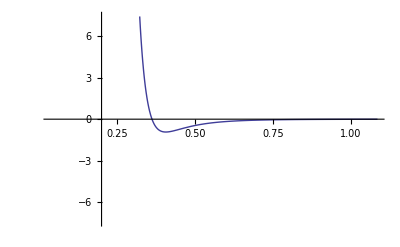

```mathematica
u[r_]:=4*ϵ*((σ/r)^12-(σ/r)^6);
f[r_]:=-D[u[r],r];
ϵ=0.929;
σ=0.362;
Plot[{u[r],f[r]},{r,0.1σ,3σ},
PlotRange->{-8ϵ,8ϵ}]
```

```mathematica
(*fix above problems*)
```

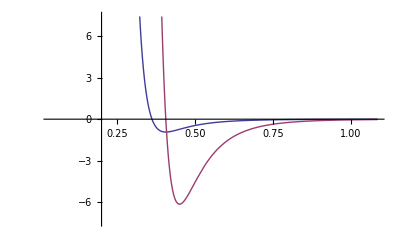

```mathematica
u[r_]:=4*ϵ*((σ/r)^12-(σ/r)^6);
f[r_]=-D[u[r],r];
ϵ=0.929;
σ=0.362;
Plot[{u[r],f[r]},{r,0.1σ,3σ},
PlotRange->{-8ϵ,8ϵ}]
```

```mathematica
(*another way*)
```

```mathematica
u[r_]:=4*ϵ*((σ/r)^12-(σ/r)^6);
f[r_]:=-D[u[r],r];
ϵ=0.929;
σ=0.362;
Plot[{u[r],f[s]/.s->r},{r,0.1σ,3σ},
PlotRange->{-8ϵ,8ϵ}]
```

-Graphics-

```mathematica
(*Evalute*)
```

```mathematica
u[r_]:=4*ϵ*((σ/r)^12-(σ/r)^6);
f[r_]:=Evaluate[-D[u[r],r]];
ϵ=0.929;
σ=0.362;
Plot[{u[r],f[r]},{r,0.1σ,3σ},
PlotRange->{-8ϵ,8ϵ}]
```

-Graphics-

```mathematica
(*
y=∫f'(x)dx anti-derivative;
*)
```

```mathematica
Integrate[x^2,x]
```

x^3/3

```mathematica
Integrate[Cos[x],x]
```

Sin[x]

```mathematica
f[x_]:=1/x;
Integrate[f[x],x]
```

Log[x]

```mathematica
Integrate[Log[x],x]
```

-x+x Log[x]

```mathematica
Integrate[ArcTan[x],x]
```

x ArcTan[x]-1/2 Log[1+x^2]

```mathematica
∫ⅇ^x Sin[b x]ⅆx
```

(ⅇ^x (-b Cos[b x]+Sin[b x]))/(1+b^2)

```mathematica
(*indefinite integral*)
```

```mathematica
Integrate[Cos[x^2],x]
```

√(π/2) FresnelC[√(2/π) x]

```mathematica
?FresnelC
```

FresnelC[z] 给出菲涅耳积分 C(z).

```mathematica
∫√ArcTan[x] ⅆx
```

∫√ArcTan[x]ⅆx

```mathematica
Integrate[1-x^2,{x,0,5}]
```

-110/3

```mathematica
∫_0^(2Pi) Sin[x]^2 ⅆx
```

π

```mathematica
(*improper integral*)
```

```mathematica
∫_(-∞)^∞ ⅇ^(-a x^2)ⅆx
```

ConditionalExpression[(√π)/(√a),Re[a]>0]

```mathematica
?ConditionalExpression
```

ConditionalExpression[expr,cond] 是一个符号结构，当条件 cond 为 True 时，表示为表达式 expr.

```mathematica
Integrate[ⅇ^(-a x^2),{x,-∞,∞},
Assumptions->{a>0}]
```

(√π)/(√a)

```mathematica
Assuming[a>0,Integrate[ⅇ^(-a x^2),{x,-∞,∞}]]
```

(√π)/(√a)

```mathematica
∫1/xⅆx
```

Log[x]

```mathematica
(*infinity integral*)
```

```mathematica
∫_1^∞ 1/xⅆx
```

Integrate::idiv: Integral of 1/x does not converge on {1, ∞}.

∫_1^∞ 1/x ⅆx

```mathematica
f[t_]:=a+b t+c t^2;
Integrate[f[t],{t,0,x}]
```

a x+(b x^2)/2+(c x^3)/3

```mathematica
Integrate[√ArcTan[x],{x,0,1}]
```

∫_0^1 √ArcTan[x]ⅆx

```mathematica
NIntegrate[√ArcTan[x],{x,0,1}]
```

0.629823

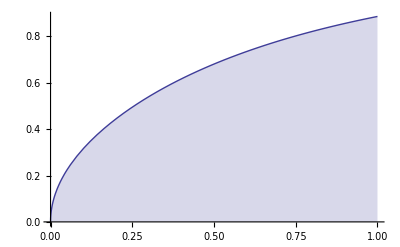

```mathematica
Plot[√ArcTan[x],{x,0,1},Filling->Axis]
```

```mathematica
(*
PV work;
ⅆW=-PⅆV;
W>0 (work is done on a system);
W<0 (work is done by a system);
compression: ⅆV<0, ⅆW>0;
Subscript[V, 1]->Subscript[V, 2]:W=-∫_Subscript[V, 1]^Subscript[V, 2] P(V)ⅆV;
van der Waals:P=nRT/(V-nb)-a(n/V)^2;
*)
```

```mathematica
p[v_]:=n r t / (v-n b) -a (n/v)^2;
w=Integrate[p[v],{v,v1,v2}]
```

ConditionalExpression[-n ((a n)/v1+r t Log[-b n+v1])+n ((a n)/v2+r t Log[-b n+v2]),((Im[v1]≥Im[v2]&&Im[v2] Re[v1]≤Im[v1] Re[v2])||(Im[v2] Re[v1]≥Im[v1] Re[v2]&&Im[v1]≤Im[v2]))&&((Re[v1/(-v1+v2)]≥0&&v1≠0&&v1^2≠v1 v2)||v1/(v1-v2)∉Reals||Re[v1/(v1-v2)]≥1)&&(v1/(v1-v2)∉Reals||Re[v1/(v1-v2)]≥1||Re[v1/(-v1+v2)]≥0)&&((-b n+v1)/(v1-v2)∉Reals||Re[(-b n+v1)/(v1-v2)]==0||Re[(-b n+v1)/(v1-v2)]≥1||Re[(b n-v1)/(v1-v2)]≥0)&&((b n-v1)/(v1-v2)∉Reals||(-b n+v1)/(v1-v2)∉Reals||Re[(b n-v1)/(v1-v2)]≤-1||Re[(b n-v1)/(v1-v2)]≥0||Re[(-b n+v1)/(v1-v2)]==0)]

```mathematica
w=Integrate[p[v],{v,v1,v2},
Assumptions->{v1>0,v2>v1,n>0,r>0,t>0,b>0,v1>n b,v2>n b}]
```

n (a n (-1/v1+1/v2)-r t Log[-b n+v1]+r t Log[-b n+v2])

```mathematica
(*
P-I-B;
Subscript[ψ, n](x)=A sin(nπx/L);
∫_0^L |Subscript[ψ, n](x)|^2 ⅆx=1=A^2∫_0^L sin^2(nπx/L)ⅆx
*)
```

```mathematica
ψ[x_]:=Sin[n π x/l];
```

```mathematica
a= Sqrt[1/Integrate[ψ[x]^2,{x,0,1}]]
```

√π √(n/(l-l Cos[(n π)/l]))

```mathematica
a= Sqrt[1/Assuming[n∈Integers,Integrate[ψ[x]^2,{x,0,l}]]]
```

√2 √(1/l)

```mathematica
(*
p(x)ⅆx=prob. var is b/w x->x+ⅆx;
∫_(All Space) p(x)ⅆx
<f(x)>=∫f(x)p(x)ⅆx;
*)
```